```mathematica
FileNameForTuple[{3,5,7}]
```

d:\triangle\DataSrc\3\5\7\Solutions.txt

```mathematica
l = DeleteDuplicates[ ReadList[FileNameForTuple[{5,7,11}],Number,100]]
```

{0,1,2,56,57,155,156,157,3150,3151,3157,3160,20000,20001,20002,20251,20252,34650,34651,34652,176302,176310,176311,176312,878880,878881,881280,881281,881287,881510,881511,881512,881531,881532,20001425,20001432,20003775,20003776,20003777,20003875,20006261,20006262,20006275,20006276,20006310,20017151,20017152,20017186,20017187,20034630,20034631,20034632,58625275,58625281,58625282,58625625,58625626,58628130,58628131,58628132,58628306,58628307,58628311,58628375,58628376,58628377,58628405,58628410,98141561,98141562,98141905,98141906,98141912,98141925,98141926,98141927,98156311,98156312,98156410,98156411,98156425,98156432,98157752,98157755,98157787,98157801,99707027,99707030,99707036,99707037,99707062,99707160,99707161,99707162,99707181,99707182,99767052,99767055,99769505,99769510}

```mathematica
l
```

{0,1,10,10,756,757,3160,3186,3187,3250}

```mathematica
strings=With[
{tuple={3,5,7}, max=50},
With[
{good=Select[DeleteDuplicates[ ReadList[FileNameForTuple[tuple],Number,max]],#>Max[tuple]&], p=First[tuple]},
Table[
StringJoin[Map[ToString[#]&,IntegerDigits[v,p]]], {v,good}
]
]
]
```

{101,1001000,1001001,11100001,11101000,11101001,11110101,101101000,101101001,101111101,1000110000,11011001101000110,11011001101001100,11101011001010110100000,11101011011111010001000,1011011100000010101000011000110,11111101101010110100111111001011010,11111101101010110100111111001011011,11111101101010110100111111001011100,11111101101010111010001110000000010,11111101101010111010001110000000011,11111101101010111010001110000011100,11111101101010111010110110101100111,11111101101010111010110111010000010,11111101101010111010110111010001011,11111110011011000000011010000110100,11111110011011000000011010000110101,11111110011011000000011010000111010,11111110011011000000011010000111011,11111110011011000000011010001111000,11111110011011000000011010001111010,11111110011011000000011010001111100,11111110011011000000011010001111101,11111110011011000000011011000001000,11111110011011000000011011000101000,11111110011011000000011011000101001,11111110100000101011101000100111101,11111110100000101011101000100111111,11111110100000101011101000101111011,11111110100000101011101000101111100,11111110100000101011101000101111101,11111010100011001110001010010101100101,11111010100011001110011101010101110001,11111010100011001110011101010111100101,11111010100011001110011101011100100000,11111010100011001110011101110001111011,11111010100011001110011101110001111111}

```mathematica
EndsWith[small_,full_] := Module[{pos},
pos=StringPosition[full,small];
If [Length[pos]==0,
Return[False],
Return[Last[Last[pos]]==StringLength[full]
]
]
]
```

```mathematica
EndWith["3","43"]
```

2

2

True

```mathematica
g=With[
{tuple={3,5,7}, max=10000},
With[
{good=Select[DeleteDuplicates[ ReadList[FileNameForTuple[tuple],Number,max]],#>Max[tuple]&], p=First[tuple]},
Module[
{i,j, strings=Table[
StringJoin[Map[ToString[#]&,IntegerDigits[v,p]]], {v,good}
],result},
result={};
Monitor[
For[i=1,i≤Length[strings], i++,
For[j=Length[strings], j≥ i+1, j--,
If[EndsWith[strings[[i]], strings[[j]]],
AppendTo[result,i->j]
]
]
],
{i,j}
];
result
]
]
]
```

{1→9990,1→9987,1→9984,1→9979,1→9975,1→9958,1→9930,1→9919,1→9899,1→9890,1→9884,1→9872,1→9862,1→9854,1→9828,1→9824,1→9801,1→9798,1→9774,1→9770,1→9766,1→9760,1→9744,1→9739,1→9734,1→9710,1→9704,1→9695,1→9682,1→9652,1→9640,1→9616,1→9614,1→9609,1→9608,1→9601,1→9600,1→9591,1→9586,1→9570,1→9552,1→9544,1→9525,1→9520,1→9511,1→9505,1→9501,1→9494,1→9492,1→9480,1→9467,1→9462,1→9460,1→9458,1→9455,1→9451,1→9440,1→9437,1→9432,1→9427,1→9421,1→9417,1→9415,1→9414,1→9407,1→9402,1→9401,1→9397,1→9379,1→9369,1→9358,1→9354,1→9352,1→9351,1→9348,1→9338,1→9333,1→9324,1→9315,1→9307,1→9282,1→9276,1→9270,1→9264,1→9258,1→9256,1→9255,1→9234,1→9227,1→9222,1→9217,1→9208,1→9203,1→9196,1→9185,1→9167,1→9166,1→9161,1→9150,1→9141,1→9137,1→9131,1→9124,1→9122,1→9118,1→9088,1→9081,1→9073,1→9030,1→9024,1→9013,1→9010,1→9008,1→9000,1→8989,1→8976,1→8972,1→8956,1→8944,1→8940,1→8934,1→8927,1→8923,1→8920,1→8901,1→8893,1→8884,1→8880,1→8876,1→8874,1→8871,1→8861,1→8858,1→8846,1→8844,1→8831,1→8819,1→8818,1→8816,1→8815,1→8808,1→8807,1→8787,1→8777,1→8775,1→8763,1→8749,1→8747,1→8745,1→8744,1→8729,1→8726,1→8716,1→8715,1→8701,1→8684,1→8678,1→8677,1→8670,1→8667,1→8663,1→8662,1→8651,1→8641,1→8631,1→8621,1→8618,1→8615,1→8601,1→8590,1→8589,1→8587,1→8571,1→8563,1→8559,1→8544,1→8539,1→8536,1→8533,1→8524,1→8518,1→8515,1→8513,1→8510,1→8495,1→8486,1→8477,1→8462,1→8460,1→8453,1→8451,1→8432,1→8424,1→8420,1→8413,1→8407,1→8403,1→8394,1→8392,1→8377,1→8366,1→8361,1→8354,1→8353,1→8348,1→8343,1→8334,1→8319,1→8316,1→8313,1→8305,1→8297,1→8280,1→8272,1→8252,1→8241,1→8233,1→8229,1→8222,1→8217,1→8208,1→8191,1→8181,1→8169,1→8163,1→8160,1→8157,1→8150,1→8128,1→8117,1→8114,1→8108,1→8102,1→8095,1→8092,1→8084,1→8083,1→8065,1→8060,1→8053,1→8034,1→8025,1→8017,1→8010,1→8003,1→7989,1→7983,1→7970,1→7969,1→7961,1→7954,1→7952,1→7934,1→7923,1→7915,1→7908,1→7896,1→7883,1→7876,1→7869,1→7858,1→7852,1→7850,1→7842,1→7828,1→7799,1→7795,1→7783,1→7780,1→7771,1→7768,1→7767,1→7754,1→7747,1→7739,1→7726,1→7718,1→7710,1→7706,1→7704,1→7680,1→7675,1→7663,1→7662,1→7659,1→7646,1→7639,1→7632,1→7625,1→7617,1→7608,1→7607,1→7602,1→7595,1→7588,1→7585,1→7582,1→7580,1→7578,1→7569,1→7558,1→7553,1→7545,1→7534,1→7526,1→7524,1→7522,1→7506,1→7491,1→7479,1→7471,1→7459,1→7456,1→7450,1→7446,1→7439,1→7422,1→7410,1→7406,1→7387,1→7370,1→7360,1→7351,1→7346,1→7322,1→7320,1→7310,1→7285,1→7275,1→7268,1→7261,1→7259,1→7249,1→7245,1→7244,1→7242,1→7235,1→7234,1→7229,1→7228,1→7225,1→7221,1→7202,1→7196,1→7181,1→7177,1→7171,1→7168,1→7159,1→7153,1→7148,1→7147,1→7131,1→7116,1→7110,1→7107,1→7097,1→7090,1→7084,1→7071,1→7064,1→7060,1→7049,1→7044,1→7041,1→7040,1→7034,1→7006,1→7001,1→6995,1→6987,1→6982,1→6964,1→6963,1→6946,1→6944,1→6933,1→6931,1→6924,1→6922,1→6887,1→6877,1→6861,1→6856,1→6842,1→6836,1→6832,1→6828,1→6826,1→6823,1→6811,1→6800,1→6782,1→6771,1→6766,1→6764,1→6761,1→6758,1→6745,1→6719,1→6707,1→6706,1→6674,1→6659,1→6654,1→6650,1→6631,1→6629,1→6624,1→6616,1→6610,1→6597,1→6586,1→6584,1→6577,1→6573,1→6570,1→6561,1→6558,1→6557,1→6550,1→6527,1→6522,1→6510,1→6508,1→6506,1→6497,1→6493,1→6486,1→6485,1→6473,1→6469,1→6457,1→6452,1→6428,1→6415,1→6402,1→6395,1→6387,1→6384,1→6365,1→6361,1→6360,1→6357,1→6345,1→6339,1→6326,1→6322,1→6317,1→6310,1→6306,1→6296,1→6293,1→6288,1→6283,1→6276,1→6273,1→6269,1→6266,1→6265,1→6263,1→6255,1→6246,1→6244,1→6239,1→6236,1→6228,1→6218,1→6204,1→6203,1→6194,1→6189,1→6185,1→6169,1→6161,1→6156,1→6139,1→6126,1→6114,1→6099,1→6057,1→6031,1→6030,1→6027,1→6020,1→6008,1→6005,1→5998,1→5983,1→5977,1→5973,1→5969,1→5968,1→5961,1→5959,1→5955,1→5949,1→5935,1→5924,1→5916,1→5908,1→5890,1→5889,1→5884,1→5880,1→5874,1→5868,1→5863,1→5850,1→5847,1→5837,1→5825,1→5807,1→5798,1→5793,1→5766,1→5749,1→5747,1→5744,1→5735,1→5733,1→5730,1→5728,1→5724,1→5723,1→5719,1→5718,1→5704,1→5695,1→5694,1→5683,1→5677,1→5666,1→5649,1→5647,1→5636,1→5633,1→5630,1→5626,1→5620,1→5611,1→5601,1→5594,1→5582,1→5571,1→5567,1→5557,1→5552,1→5546,1→5542,1→5524,1→5522,1→5513,1→5506,1→5503,1→5473,1→5469,1→5467,1→5458,1→5454,1→5440,1→5433,1→5426,1→5425,1→5418,1→5415,1→5411,1→5409,1→5407,1→5400,1→5397,1→5387,1→5376,1→5369,1→5368,1→5358,1→5351,1→5337,1→5327,1→5324,1→5319,1→5297,1→5295,1→5277,1→5272,1→5260,1→5231,1→5229,1→5209,1→5207,1→5203,1→5200,1→5196,1→5191,1→5184,1→5179,1→5173,1→5171,1→5153,1→5139,1→5131,1→5128,1→5122,1→5108,1→5105,1→5095,1→5089,1→5086,1→5077,1→5065,1→5062,1→5059,1→5041,1→5032,1→5021,1→5018,1→5017,1→5008,1→5001,1→4993,1→4991,1→4990,1→4979,1→4976,1→4971,1→4955,1→4949,1→4948,1→4939,1→4934,1→4926,1→4920,1→4919,1→4913,1→4905,1→4900,1→4888,1→4881,1→4873,1→4870,1→4849,1→4842,1→4826,1→4805,1→4804,1→4799,1→4790,1→4787,1→4783,1→4770,1→4757,1→4738,1→4736,1→4735,1→4728,1→4706,1→4703,1→4699,1→4689,1→4678,1→4676,1→4672,1→4671,1→4664,1→4659,1→4658,1→4646,1→4645,1→4639,1→4632,1→4616,1→4605,1→4602,1→4576,1→4570,1→4547,1→4541,1→4530,1→4528,1→4524,1→4520,1→4506,1→4500,1→4490,1→4486,1→4481,1→4476,1→4461,1→4454,1→4450,1→4448,1→4443,1→4435,1→4432,1→4426,1→4418,1→4413,1→4408,1→4392,1→4389,1→4386,1→4366,1→4358,1→4356,1→4343,1→4341,1→4330,1→4318,1→4302,1→4300,1→4297,1→4291,1→4289,1→4287,1→4281,1→4263,1→4230,1→4228,1→4227,1→4213,1→4196,1→4194,1→4189,1→4185,1→4173,1→4151,1→4140,1→4134,1→4128,1→4127,1→4119,1→4112,1→4096,1→4088,1→4086,1→4075,1→4059,1→4053,1→4052,1→4042,1→4025,1→4010,1→4007,1→4002,1→3995,1→3993,1→3971,1→3967,1→3966,1→3963,1→3957,1→3951,1→3943,1→3924,1→3921,1→3918,1→3910,1→3906,1→3901,1→3897,1→3891,1→3882,1→3879,1→3870,1→3842,1→3832,1→3829,1→3816,1→3815,1→3810,1→3800,1→3799,1→3792,1→3776,1→3774,1→3771,1→3759,1→3741,1→3739,1→3722,1→3719,1→3706,1→3699,1→3694,1→3686,1→3651,1→3642,1→3638,1→3636,1→3630,1→3615,1→3609,1→3607,1→3602,1→3596,1→3586,1→3584,1→3582,1→3578,1→3573,1→3569,1→3561,1→3549,1→3542,1→3538,1→3516,1→3512,1→3505,1→3492,1→3489,1→3475,1→3470,1→3462,1→3459,1→3451,1→3442,1→3436,1→3419,1→3405,1→3390,1→3385,1→3377,1→3375,1→3372,1→3366,1→3363,1→3353,1→3349,1→3346,1→3340,1→3334,1→3325,1→3309,1→3307,1→3286,1→3282,1→3280,1→3279,1→3270,1→3267,1→3257,1→3252,1→3244,1→3242,1→3236,1→3228,1→3226,1→3223,1→3214,1→3199,1→3195,1→3187,1→3182,1→3177,1→3162,1→3156,1→3153,1→3151,1→3147,1→3139,1→3132,1→3126,1→3123,1→3096,1→3092,1→3090,1→3085,1→3081,1→3079,1→3070,1→3069,1→3067,1→3063,1→3057,1→3051,1→3045,1→3040,1→3037,1→3032,1→3025,1→3017,1→2998,1→2986,1→2975,1→2972,1→2968,1→2956,1→2952,1→2942,1→2934,1→2921,1→2915,1→2913,1→2909,1→2904,1→2882,1→2855,1→2848,1→2844,1→2838,1→2831,1→2820,1→2804,1→2798,1→2784,1→2775,1→2773,1→2745,1→2727,1→2714,1→2713,1→2707,1→2695,1→2681,1→2669,1→2650,1→2642,1→2641,1→2629,1→2624,1→2609,1→2603,1→2597,1→2595,1→2586,1→2575,1→2560,1→2555,1→2554,1→2550,1→2541,1→2534,1→2530,1→2529,1→2510,1→2509,1→2499,1→2493,1→2486,1→2482,1→2464,1→2456,1→2449,1→2428,1→2423,1→2418,1→2414,1→2405,1→2400,1→2396,1→2383,1→2380,1→2374,1→2367,1→2366,1→2362,1→2358,1→2357,1→2352,1→2347,1→2344,1→2339,1→2336,1→2326,1→2312,1→2307,1→2304,1→2299,1→2297,1→2295,1→2292,1→2270,1→2266,1→2264,1→2255,1→2249,1→2240,1→2235,1→2231,1→2224,1→2216,1→2195,1→2194,1→2177,1→2161,1→2158,1→2147,1→2141,1→2123,1→2119,1→2114,1→2110,1→2099,1→2087,1→2079,1→2066,1→2062,1→2061,1→2058,1→2057,1→2053,1→2043,1→2041,1→2038,1→2034,1→2027,1→2017,1→2003,1→2002,1→1990,1→1985,1→1973,1→1964,1→1958,1→1956,1→1941,1→1934,1→1913,1→1910,1→1888,1→1884,1→1869,1→1857,1→1849,1→1847,1→1843,1→1840,1→1825,1→1813,1→1812,1→1805,1→1790,1→1765,1→1758,1→1756,1→1739,1→1732,1→1723,1→1722,1→1717,1→1713,1→1701,1→1686,1→1683,1→1670,1→1662,1→1661,1→1648,1→1643,1→1639,1→1630,1→1627,1→1624,1→1614,1→1608,1→1601,1→1599,1→1593,1→1585,1→1579,1→1573,1→1572,1→1567,1→1559,1→1553,1→1545,1→1542,1→1525,1→1518,1→1512,1→1504,1→1502,1→1496,1→1492,1→1487,1→1470,1→1464,1→1459,1→1443,1→1439,1→1410,1→1404,1→1400,1→1397,1→1390,1→1379,1→1368,1→1359,1→1354,1→1352,1→1329,1→1324,1→1308,1→1294,1→1291,1→1281,1→1269,1→1267,1→1260,1→1251,1→1248,1→1244,1→1241,1→1232,1→1219,1→1215,1→1210,1→1204,1→1199,1→1196,1→1193,1→1178,1→1166,1→1136,1→1128,1→1125,1→1122,1→1106,1→1096,1→1095,1→1091,1→1088,1→1083,1→1074,1→1068,1→1052,1→1049,1→1044,1→1042,1→1036,1→1035,1→1032,1→1014,1→1002,1→996,1→991,1→981,1→980,1→968,1→964,1→955,1→936,1→930,1→928,1→917,1→914,1→908,1→903,1→898,1→890,1→883,1→881,1→876,1→868,1→864,1→858,1→856,1→843,1→825,1→820,1→816,1→801,1→790,1→785,1→782,1→772,1→760,1→754,1→752,1→747,1→743,1→727,1→722,1→712,1→710,1→706,1→704,1→700,1→695,1→689,1→687,1→682,1→669,1→659,1→652,1→635,1→619,1→613,1→603,1→597,1→592,1→587,1→585,1→574,1→572,1→569,1→563,1→540,1→536,1→519,1→507,1→494,1→488,1→484,1→481,1→476,1→466,1→456,1→450,1→442,1→441,1→434,1→421,1→412,1→404,1→396,1→386,1→378,1→373,1→370,1→363,1→357,1→315,1→310,1→306,1→287,1→286,1→283,1→275,1→273,1→243,1→240,1→237,1→233,1→212,1→205,1→203,1→199,1→195,1→191,1→187,1→183,1→165,1→161,1→155,1→151,1→148,1→133,1→130,1→125,1→123,1→118,1→106,1→97,1→89,1→71,1→66,1→62,1→55,1→51,1→44,1→42,1→41,1→37,1→33,1→27,1→10,1→7,2→9669,2→9529,2→9385,2→9240,2→9103,2→9015,2→8913,2→8851,2→8784,2→8482,2→8245,2→8197,2→8190,2→7676,2→7640,2→7282,2→7037,2→6950,2→6939,2→6647,2→6518,2→6460,2→6432,2→6318,2→6311,2→6180,2→6151,2→6091,2→6036,2→5751,2→5591,2→5568,2→5518,2→5447,2→5430,2→5405,2→5312,2→4897,2→4610,2→4514,2→4468,2→4203,2→4054,2→3683,2→3619,2→3506,2→3111,2→2811,2→2732,2→2570,2→2531,2→2479,2→2218,2→2132,2→1993,2→1720,2→1691,2→1453,2→1423,2→1375,2→1286,2→1268,2→1144,2→1012,2→865,2→810,2→606,2→401,2→380,2→340,2→336,2→92,3→9298,3→9296,3→9241,3→9104,3→8852,3→8830,3→8566,3→8483,3→8425,3→8246,3→8198,3→8007,3→7831,3→7731,3→7641,3→7620,3→7510,3→7417,3→7038,3→6951,3→6869,3→6648,3→6519,3→6319,3→6181,3→6083,3→6037,3→5986,3→5947,3→5929,3→5752,3→5592,3→5569,3→5470,3→5448,3→5431,3→5406,3→5313,3→4611,3→4597,3→4469,3→4242,3→4055,3→4026,3→4018,3→3684,3→3670,3→3507,3→3391,3→3125,3→3112,3→2733,3→2532,3→2406,3→2385,3→2164,3→1994,3→1794,3→1721,3→1692,3→1535,3→1472,3→1454,3→1388,3→1237,3→866,3→607,3→337,3→252,3→63,4→9846,4→9536,4→9471,4→8269,4→8138,4→8109,4→8055,4→7699,4→7653,4→7359,4→7157,4→6729,4→6715,4→6604,4→6501,4→5713,4→5669,4→5396,4→5147,4→4628,4→3914,4→3692,4→3618,4→3524,4→2592,4→2420,4→2184,4→1880,4→1715,4→1642,4→994,4→686,4→552,4→347,4→335,4→215,4→207,4→159,5→9787,5→9685,5→9411,5→9343,5→9273,5→8723,5→7994,5→7590,5→6941,5→6798,5→6730,5→6721,5→6581,5→6563,5→6157,5→6044,5→5817,5→5673,5→5608,5→4796,5→4478,5→4458,5→4393,5→4362,5→4235,5→4107,5→3931,5→3821,5→2696,5→2600,5→2095,5→1780,5→1768,5→1142,5→783,5→657,5→633,5→601,5→589,5→553,5→538,5→520,5→360,5→196,6→9878,6→9788,6→9686,6→9473,6→9412,6→9344,6→9040,6→8724,6→8209,6→7995,6→7419,6→6867,6→6852,6→6799,6→6731,6→6722,6→6582,6→6077,6→5674,6→5609,6→4797,6→4459,6→4394,6→4363,6→4236,6→4108,6→3322,6→2780,6→2697,6→2523,6→2096,6→1769,6→1363,6→1143,6→784,6→658,6→634,6→602,6→590,6→539,6→361,6→197,7→9609,7→9379,7→7842,7→7718,7→6964,7→6931,7→6761,7→6674,7→6629,7→6322,7→6317,7→6114,7→6020,7→5924,7→5744,7→5718,7→5694,7→5567,7→5513,7→4979,7→4948,7→4873,7→4849,7→4196,7→3906,7→3489,7→3177,7→3126,7→2347,7→2339,7→2312,7→2114,7→1294,7→1251,7→106,7→62,8→9304,8→8611,8→8537,8→7987,8→7887,8→7684,8→7482,8→5963,8→5684,8→5658,8→4944,8→4284,8→4273,8→4159,8→4156,8→3826,8→3517,8→3409,8→3301,8→3101,8→2876,8→2489,8→2049,8→297,9→9459,9→9230,9→9062,9→8612,9→7988,9→7888,9→7685,9→7362,9→6504,9→5685,9→5659,9→5080,9→4945,9→4157,9→3827,9→3468,9→3410,9→3302,9→2898,9→2490,9→1589,9→99,10→9704,10→9614,10→9480,10→9122,10→9010,10→8252,10→7989,10→7171,10→6987,10→6832,10→6610,10→6586,10→6508,10→5747,10→5647,10→5351,10→5077,10→3829,10→2934,10→1035,10→619,10→536,10→212,10→41,11→9404,11→9108,11→8958,11→8368,11→6129,11→5445,11→4324,11→388}

```mathematica
Needs["Combinatorica`"]
```

```mathematica
Needs["Combinatorica`"]
```

Needs[Combinatorica`]

```mathematica
Needs["Combinatorica`"]
```

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
Kruskal
```

```mathematica
NumberOfSpanningTrees[CompleteGraph[3,3]]
```

81

```mathematica
MinimumSpanningTree[{1->2,1->3,2->1}]
```

```mathematica
ShortestPathSpanningTree[{1->2,1->3,2->1},1]
```

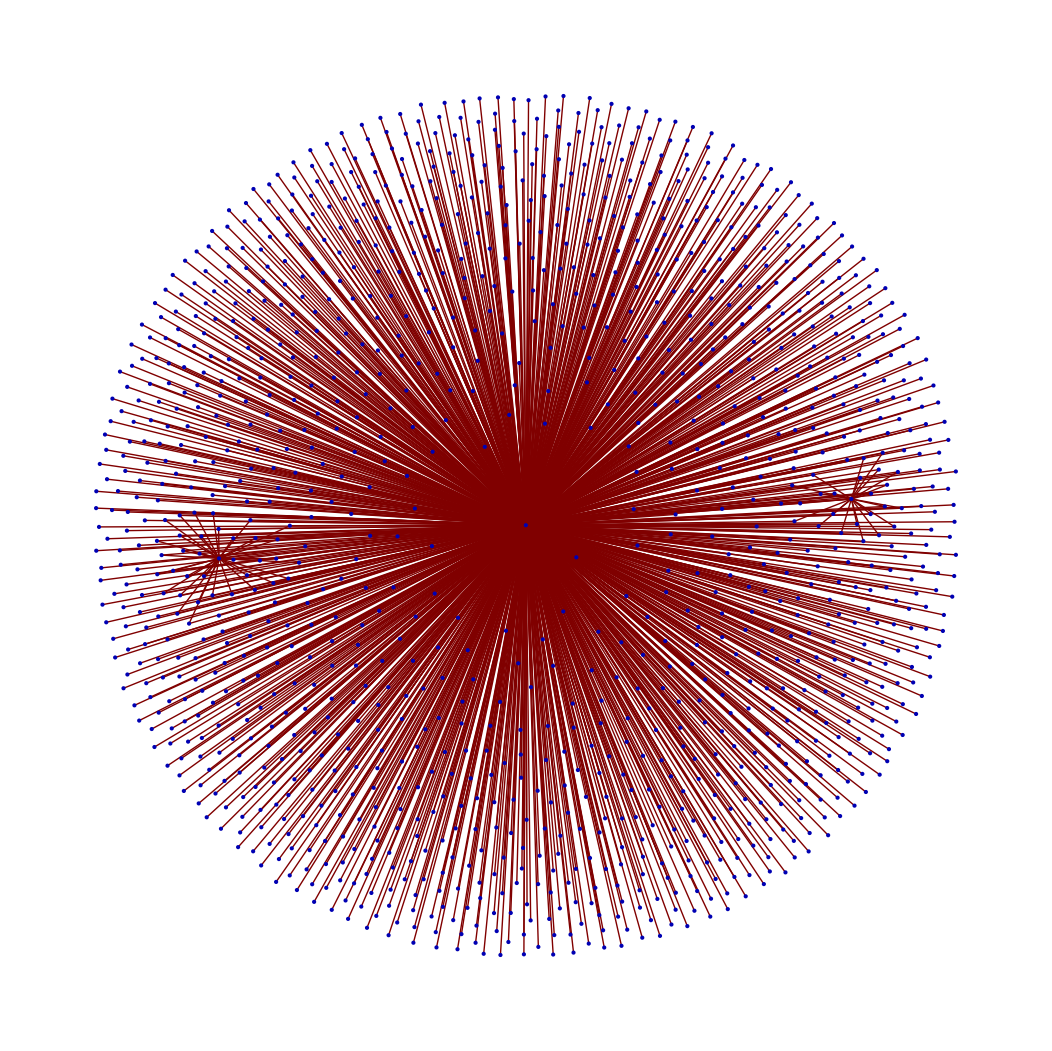

```mathematica
GraphPlot[NeighborhoodSubgraph[ToCombinatoricaGraph[g],1]]
```

```mathematica
gc=ToCombinatoricaGraph[g]
```

⁃Graph:<1648,1597,Directed>⁃

```mathematica
NumberOfSpanningTrees[NeighborhoodSubgraph[ gc,1]]
```

0

```mathematica
mst=MinimumSpanningTree[NeighborhoodSubgraph[ gc,1]]
```

MinimumSpanningTree[⁃Graph:<1328,1269,Directed>⁃]

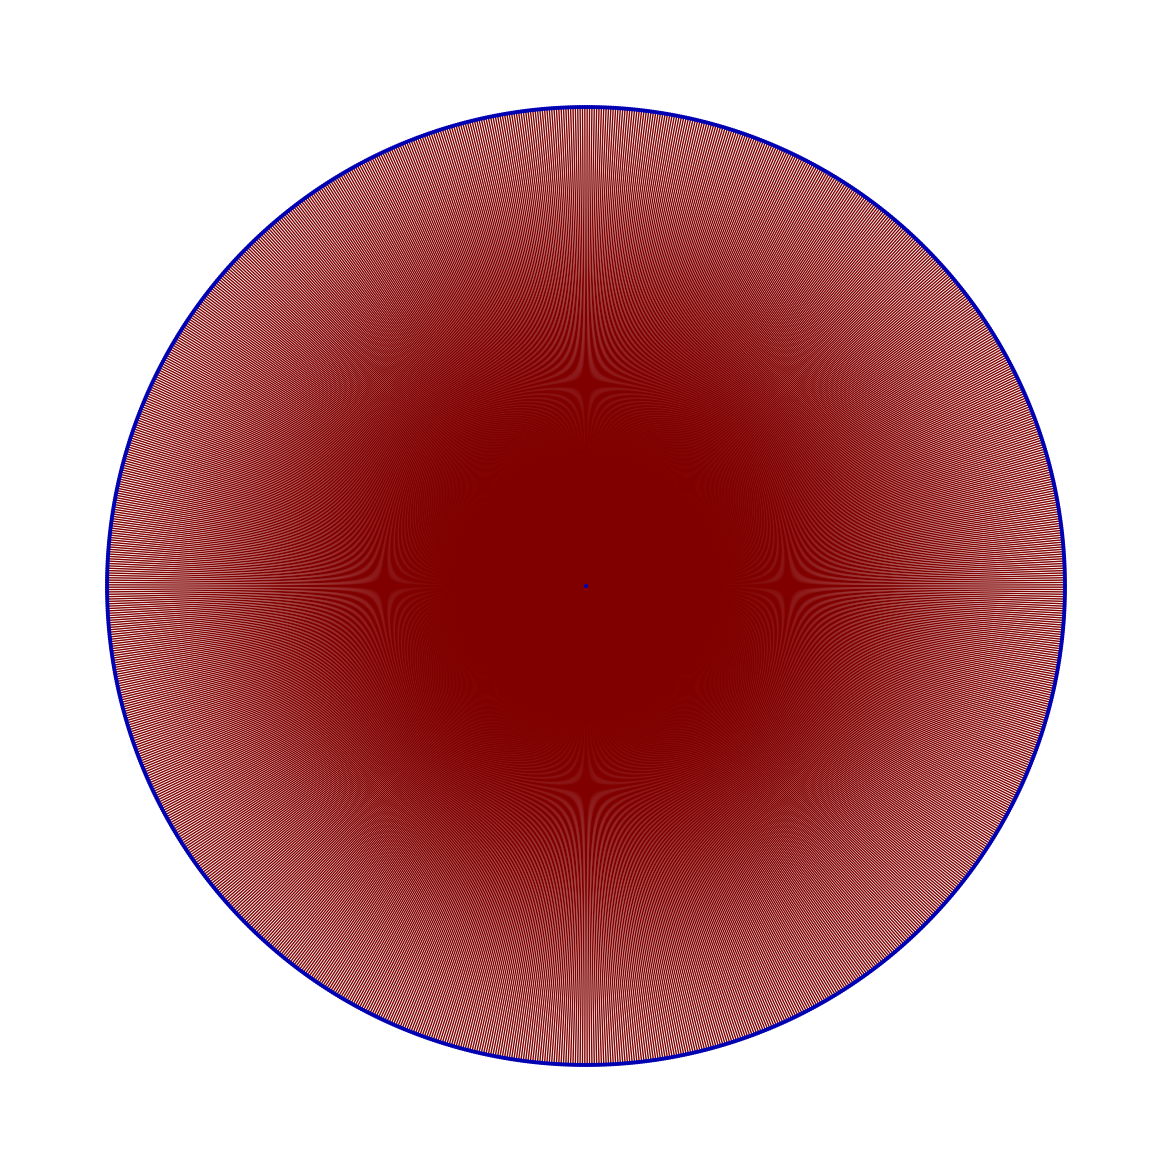

```mathematica
GraphPlot[MaximumSpanningTree[NeighborhoodSubgraph[ gc,1]]]
```

```mathematica
FerrersDiagram[g]
```

FerrersDiagram[g]

```mathematica
TableForm[RandomTableau[{6,5,5,4,3,2}]]
```

1 | 2 | 3 | 7 | 16 | 18
4 | 5 | 10 | 15 | 21 | 
6 | 8 | 11 | 17 | 25 | 
9 | 12 | 13 | 23 |  | 
14 | 19 | 20 |  |  | 
22 | 24 |  |  |  |

```mathematica
AnimateGraph[CompleteGraph[3,3],1]
```

AnimateGraph[⁃Graph:<9,6,Undirected>⁃,1]

```mathematica
GraphQ[g]
```

GraphQ[g]

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

```mathematica
GraphPlot[FromAdjacencyMatrix[AdjacencyMatrix[g]]]
```

GraphPlot::grph: FromAdjacencyMatrix[TagBox[SparseArray[« 1 »], False, Rule[Editable, False]]] is not a valid graph.

GraphPlot[FromAdjacencyMatrix[SparseArray[<1588>,{1597,1597}]]]

```mathematica
Graph
```

```mathematica
p=FromAdjacencyList[AdjacencyMatrix[g]]
```

FromAdjacencyMatrix[SparseArray[<1588>,{1597,1597}]]

```mathematica
With[
{tuple={3,5,7}, max=10000000},
With[
{good=Monitor[ReadList[FileNameForTuple[tuple],Number,max],"Reading"]
, p=First[tuple]},
Module[
{i,sample},
sample={1,1,1,1,1,1,1,0,1,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1};
Monitor[
For[i=1000000,i≤Length[good], i++,
If[ListEndsWith[sample, IntegerDigits[good[[i]],p]],
Print[good[[i]]]
]
],
i
]
]
]
]
```

```mathematica
IntegerDigits[25006879956023281,3]
```

{1,1,1,1,1,1,1,0,1,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1}

```mathematica
IntegerDigits[25006879956023281,3]
```

```mathematica
ListEndsWith[part_,whole_]:= Module[
{lp=Length[part],lw=Length[whole]},
If[lp> lw,
False,
part == Take[whole,-lp]
]
]
```

```mathematica
ListEndsWith[{1,2},{1,2,3,1,2}]
```

True

```mathematica
IntegerDigits[Select[DeleteDuplicates[ ReadList[FileNameForTuple[{3,5,7}],Number,50]],#>Max[{3,5,7}]&][[41]],3]
```

```mathematica
StringJoin[Map[ToString[#]&,{1,1,1,1,1,1,1,0,1,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,1}]]
```

11111110100000101011101000101111101

```mathematica
IntegerDigits[Select[DeleteDuplicates[ ReadList[FileNameForTuple[{3,5,7}],Number,50]],#>Max[{3,5,7}]&][[10]],3]
```

{1,0,1,1,1,1,1,0,1}

```mathematica
IntegerDigits[Select[DeleteDuplicates[ ReadList[FileNameForTuple[{3,5,7}],Number,50]],#>Max[{3,5,7}]&][[1]],3]
```

{1,0,1}

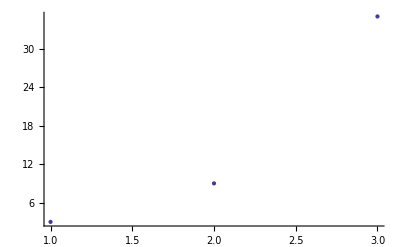

```mathematica
ListPlot[{3,9,35}]
```

```mathematica
N[Log[10,3^81]]
```

38.6468